```mathematica
.00
```

```mathematica
(*このファイルのコードでは有限要素法により拡散方程式を解いた結果の剛性行列から隣接行列を作成する*)
```

## 1~9 の数字 (+インレット) の領域を作成する

```mathematica
Clear["Global`*"]
inletPosition={{0,1.2},{0.3,2}}; (*this gives the dimensions of the inlet*)
inlet=Rectangle@@inletPosition;
listRegion=ParallelTable[
t=Text[Style[char,Bold]];
Ω=RegionUnion[inlet,#]&@TransformedRegion[#,0.5*{(Indexed[#,1]+0),(Indexed[#,2]+0)}&]&@BoundaryDiscretizeGraphics[t,_Text,MaxCellMeasure->0.03,PlotRange->All],
{char,ToString/@Range@9}];
```

#### 作成した領域の表示 （確認）

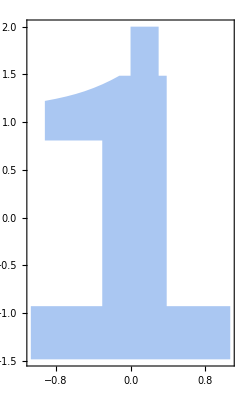
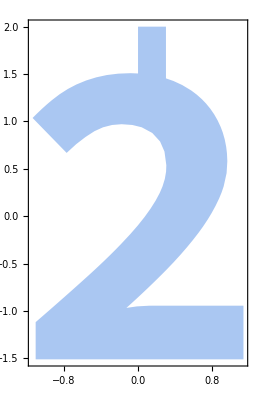
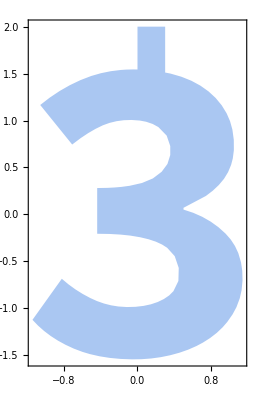
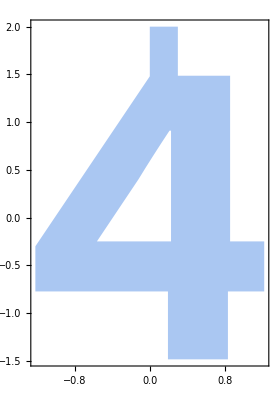
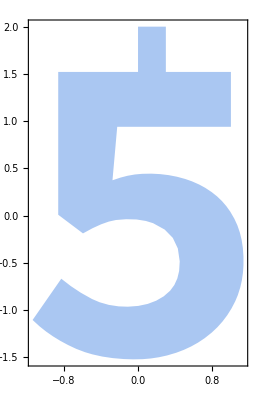
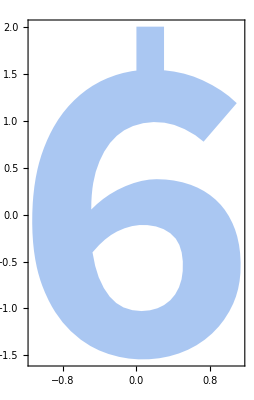
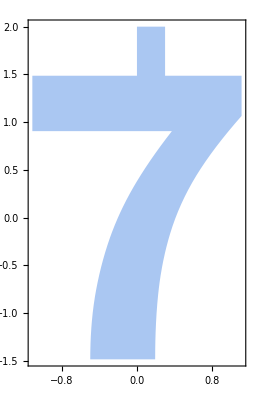
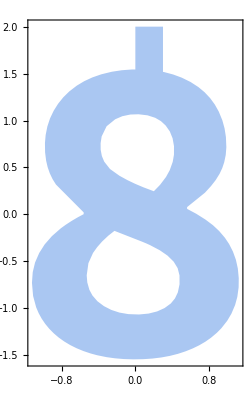

```mathematica
(*Region[#,AspectRatio->1,Frame->True]&@RegionUnion[inlet,#]&/@listRegion*)
Region[#,Frame->True]&@RegionUnion[inlet,#]&/@listRegion
```

## 作成した全領域の隣接行列を一括で作成する 数字の1~9 から生成した領域にnBeads個の点をランダムに配置し，それぞれの数字に対してnSample個の隣接行列を作る． これらの隣接行列をデータセットとして隣接行列がどの数字から得られたものかを推定するのが今回の目的．

```mathematica
(*TODO: フォルダがない場合自動生成するようにする*)
(*要素数はMaxCellMeasureを変えてもあまり変わらないので固定する*)

Needs["NDSolve`FEM`"]
SetDirectory[NotebookDirectory[]];

testRun = True;
nBeads=If[testRun, 10,1000];
nSample=If[testRun,10,100];
prefix=If[testRun,"small_",""];

valInfo=<|"use"->"val","num"->Round[nSample*0.1]|>;
testInfo=<|"use"->"test","num"->Round[nSample*0.1]|>;
trainInfo=<|"use"->"train","num"->nSample-valInfo["num"]-testInfo["num"]|>;

(*Fixed parameters*)
cellSize=0.01;
t=20;

nbd=NotebookDirectory[];
(*存在しない時はディレクトリを自動作成する*)
Table[CreateDirectory@FileNameJoin@{nbd,prefix<>"data_coords",i,"raw",j};
,{i,{"train","val","test"}},{j,{"adj","coords"}}];

timeFunc=AbsoluteTiming[
(*今回はサンプルするたびにビーズの初期位置だけをランダムに変更し，メッシュの切り方やPDEの計算結果はサンプル間で同じものを用いる*)
meshStiff=ParallelTable[
maxcellsize=cellSize;

nr=ToElementMesh[#,MaxCellMeasure->maxcellsize]&@BoundaryDiscretizeRegion@Ω;
vd=NDSolve`VariableData[{"DependentVariables"->{u},"Space"->{x,y}}];
sd=NDSolve`SolutionData[{"Space"->nr}];

coefficients={"DiffusionCoefficients"->{{IdentityMatrix[2]}},"DampingCoefficients"->{{1}}};

initCoeffs=InitializePDECoefficients[vd,sd,coefficients];
methodData=InitializePDEMethodData[vd,sd];

(*Assembly of matrices*)
discretePDE=DiscretizePDE[initCoeffs,methodData,sd];
{load,stiffness,damping,mass}=discretePDE["SystemMatrices"];

<|"mesh"->nr,"stiffMat"->stiffness|>
,{Ω,listRegion}];

generateData[k_]:=ParallelTable[
(*e-^tMを隣接行列とみなす場合は要素の頂点数と同じ数の種類のビーズを使うことを仮定している*)
(*次元が大きいと行列の指数関数を計算するのが大変なので用いたビーズの種類に次元を縮める*)
nr=meshStiff[[i]]["mesh"];
stiffness=meshStiff[[i]]["stiffMat"];
n=Length@stiffness;  (*要素数*)

exRoot=FileNameJoin[{nbd,prefix<>"data_coords",k["use"],"raw"}];
(*ファイル名につける番号．pythonで用いるので0th indexにしている．*)
fileID=k["num"]*(i-1)+j-1;
(*簡単のためビーズは接点上に配置されると仮定．要素内部への配置も認めるには濃度，座標の設定時に何かしら補完する必要がある*)
(*最初にビーズを配置する節点のインデックスを重複のないように用いるビーズの数だけランダムに選ぶ*)
iInitialPoints=RandomSample[Range[n],nBeads];
(*ビーズの座標、つまり最初に各ビーズをおく節点の座標*)
coBeads=nr["Coordinates"][[iInitialPoints]];
(*i番目のビーズの領域に初期濃度を(1,要素数)のi番目だけが1の単位ベクトルとして表している
そのような単位ベクトルをビーズの種類数だけ集めて行列Vを形成している*)
transC0=Table[UnitVector[n,iInitialPoints[[iBead]]],{iBead,nBeads}];
(*剛性行列stiffnessは(要素数,要素数)と非常に大きいのでそのまま指数行列を計算するのは大変
そこでmathematicaの機能によりあらかじめC0をかけることで次元を減らし計算量の低減している*)
transCt=Chop@MatrixExp[t*stiffness,#]&/@transC0;
(*隣接行列を計算した後，(1,ビーズ数^2)に整形し，最後にターゲットの番号(1~9)を追加する*)
A=transCt.Transpose[transCt];
(*対角成分を0にすることでループを除外する*)
A=A-DiagonalMatrix[Diagonal[A]];
(*隣接行列の1/n(定常態の時隣接行列の要素)より小さい要素を0に置き換える*)
adjMat=A/.x_/;x<1.0/n->0;
Export[FileNameJoin[{exRoot,"adj","adj_"<>ToString@fileID<>".mtx"}],SparseArray@adjMat];
Export[FileNameJoin[{exRoot,"coords","coords_"<>ToString@fileID<>".mtx"}],SparseArray@coBeads];
,{i,Range@Length@meshStiff},{j,Range@k["num"]}];

generateData[valInfo];
generateData[testInfo];
generateData[trainInfo];
];

(*実験条件・所要時間の表示*)
Print@"=====Simulation conditions====="
Print["Number of beads: "<>ToString@nBeads]
Print["Number of samples for each shape: "<>ToString@nSample]
Print["Diffusion time: "<>ToString@t]
Print["Test run: "<>ToString@testRun]
Print@"=====Calculation time======"
elapsedTime=UnitConvert[Quantity[#,"Seconds"],MixedRadix["Hours","Minutes","Seconds"]]&@timeFunc[[1]];
Print["Elapsed time: "<>ToString@elapsedTime]
```

=====Simulation conditions=====

Number of beads: 10

Number of samples for each shape: 10

Diffusion time: 20

Test run: True

=====Calculation time======

Elapsed time: 0 hours 0 minutes 9.29275 seconds

## 1 種類の図形によるテスト

```mathematica
Needs["NDSolve`FEM`"]
SetDirectory[NotebookDirectory[]];

Ω=listRegion[[1]];
maxcellsize=.4;
(*ϵ=0*0.001;
τ=0.1;*)
nr=ToElementMesh[#,MaxCellMeasure->0.1]&@BoundaryDiscretizeRegion[Ω];

vd=NDSolve`VariableData[{"DependentVariables"->{u},"Space"->{x,y,z}}];
sd=NDSolve`SolutionData[{"Space"->nr}];

coefficients={"DiffusionCoefficients"->{{IdentityMatrix[3]}},"DampingCoefficients"->{{1}}};
initCoeffs=InitializePDECoefficients[vd,sd,coefficients];
methodData=InitializePDEMethodData[vd,sd];

(*Assembly of matrices*)
discretePDE=DiscretizePDE[initCoeffs,methodData,sd];
{load,stiffness,damping,mass}=discretePDE["SystemMatrices"];

n=Length@stiffness;
V=Table[UnitVector[n,RandomInteger[{1,n}]],{40}];
Dimensions@V
R=Chop@MatrixExp[.2*stiffness,#]&/@V;
Dimensions@R
Dimensions@Transpose@R
M=R.Transpose[R]
MatrixPlot@M
am=M/.x_/;x<0->0;
Export["stiffTest.mtx",SparseArray[am]];
Dimensions@stiffness
```

## その他の確認？

```mathematica
n=Length@stiffness;
V=Table[UnitVector[n,RandomInteger[{1,n}]],{40}];
Dimensions@V
R=Chop@MatrixExp[.2*stiffness,#]&/@V;
Dimensions@R
Dimensions@Transpose@R
M=R.Transpose[R]
MatrixPlot@M
```